# 1+1 QCD with Adjoint Fermions -- Classical Limit

```mathematica
(*This code reproduces the scattering of a classical Hamiltonian describing Num identical massless particles which have a preferred ordering with respect to their immediate neighbors. It arrises as the limit of QCD in 1+1 dimensions with adjoint fermions. Questions, bugs, comments, etc can be sent to jcd484@nyu.edu*)
```

```mathematica
Num=5;
```

## Definitions

```mathematica
newrandom:=Do[a0=Sort[RandomReal[{-15,15},Num]];p0=RandomReal[{-20,20},Num];p0=Reverse[Sort[p0]];p0=Rationalize[p0,.1];a0=Rationalize[a0,.1];,1];
(*newrandom will give random rationalized inital conditions when called*)
a=Table[Subscript[x, i][t],{i,1,Num,1}];
p=Table[Subscript[v, i][t],{i,1,Num,1}];
(*We then define our confining potential*)
V[σ_]:= (First[σ]-Last[σ])+Sum[RealAbs[σ[[i]]-σ[[i+1]]],{i,1,Length[σ]-1}];
Vp[a_]:=PiecewiseExpand[V[a]];
ExRelEqs[a_,p_]:=Join[MapThread[D[#1,t]==-#2&,{p,D[Vp[a],{a}]}],MapThread[D[#1,t]== If[#2>0,1,-1]&,{a,p}]];
(*The EOM are always piecewise constant, so here we expand them*)
exacts=PiecewiseExpand[ExRelEqs[a,p]];
(*We then solve and recombine, with the nontrivial information given by the piecewise conditions*)
exsols=DSolve[#,Flatten[{a,p}],t]&/@Internal`FromPiecewise[exacts][[2]];
functions=Table[PiecewiseExpand[Internal`ToPiecewise@@{Internal`FromPiecewise[exacts][[1]],Flatten[exsols[[All,All,i,2]]]}],{i,2*Num}];
functions=Flatten[Table[{functions[[i]],functions[[Num+i]]},{i,Num}]];
(*These functions give the dynamics of each particle given a spatial ordering and momemtun signs*)
```

```mathematica
(*Evolve just does the work of choosing and gluing the different solutions found above together to give the full scattering*)
```

```mathematica
Evolve[a0_,p0_]:=Module[{},newinits=Flatten[Table[{p0[[i]],a0[[i]]},{i,Num}]];
(*Initializing variables*)
whereamigoin={a0,p0};
tinit=0;
possols={};
momsols={};
steps={};
s=0;
While[True(*Loop should break itself later*),
(*Choose the dynamics given a particle ordering*)
thisround=Simplify[functions,Join[MapThread[#1== #2&,{a,whereamigoin[[1]]}],MapThread[#1== #2&,{p,whereamigoin[[2]]}]]];
(*Match free coefficients to initial conditions*)
toinit=thisround/.t->tinit;
rationals=FullSimplify[Flatten[MapThread[Solve[#1==#2,#3,Rationals]&,{toinit,newinits,Flatten[Table[{C[i],C[i+Num]},{i,Num}]]}]]];
evolve=thisround/.rationals;
posevol=Table[evolve[[2i]],{i,Num}];
momevol=Table[evolve[[2i-1]],{i,Num}];
possols=Join[possols,{posevol}];
momsols=Join[momsols,{momevol}];
(*Find the point where the next pair of particles cross, changing the ordering and thus the dynamics*)
intersect=Quiet[Table[If[i≠j,t/.Solve[{posevol[[i]]== posevol[[j]],tinit<t},t,Rationals],{-∞}],{j,Num},{i,Num}]];
(*Or when a particle should turn around*)
intersect2=Quiet[Table[t/.Solve[{momevol[[i]]== 0,tinit<t},t,Rationals],{i,Num}]];
intersect3=Join[{Flatten[intersect],Flatten[intersect2]}];
intersect4=Flatten[intersect3/.t->{-∞}];
(*Break the loop if there are no such points, and tell the solution this extends for all time*)
If[AllTrue[Flatten[intersect4],#== -∞&],steps=Join[steps,{t>tinit}]];
If[AllTrue[Flatten[intersect4],#== -∞&],Break[]];
forward=Select[intersect4-tinit,NonNegative];
(*Choose the most immediate event*)
tinter=Min[forward];
tinter=tinit+tinter;
newinits=evolve/.t->tinter;
(*Push the solution forward an epsilon amount just so the Piecewise has no trouble choosing which sector it's in*)
whereamigoin={posevol,momevol}/.t->tinter+20000*3*10^-16;
steps=Join[steps,{tinit<t<tinter}];
tinit=FullSimplify[tinter];]];
```

## Example

```mathematica
newrandom
a0
p0
```

{-37/4,-9,-11/2,-16/3,57/8}

{59/3,55/3,47/3,13/2,-35/4}

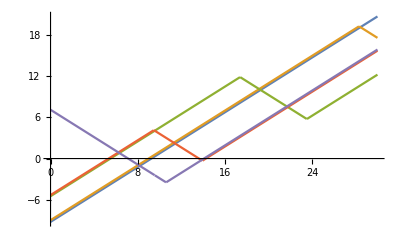

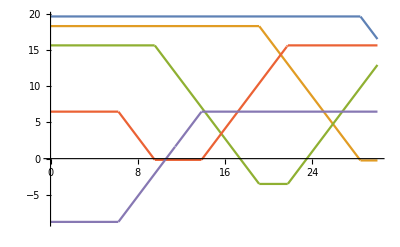

```mathematica
Evolve[a0,p0];
time=30;
posfull =Table[PiecewiseExpand[Internal`ToPiecewise@@{steps,possols[[All,i]]}],{i,Num}];
momfull =Table[PiecewiseExpand[Internal`ToPiecewise@@{steps,momsols[[All,i]]}],{i,Num}];
posplot=Plot[posfull,{t,0,time},PlotRange->Full(*,GridLines->{{Time[[l,1]],Time[[l,2]]}, {1,1}}*)]
momplot=Plot[momfull,{t,0,time}]
```

## Animation

```mathematica
vdrop=90
Animate[Show[Block[{α=posfull[[1]]-100/.t-> v,γ=Abs[α]},ParametricPlot[{s/(2π γ)*posfull[[1]]-(1-s/(2π γ))*100/.t-> v,0-v/vdrop},{s,0,2π γ},Axes->None,PlotStyle->Gray,PlotRange->{{-30,30},{-5,10}}]],Block[{α=-100-posfull[[5]]/.t-> v,γ=Abs[α]},ParametricPlot[{(1-s/(2π γ))*posfull[[5]]+(s/(2π γ))*100/.t-> v,4-v/vdrop},{s,0,2π γ},Axes->None,PlotStyle->Gray]],Block[{α=posfull[[2]]-posfull[[1]]+.01/.t-> v,γ=Abs[α]},ParametricPlot[{(1-s/(2π γ))*posfull[[1]]+s/(2π γ)*posfull[[2]]/.t-> v,0+s/(2π γ)-v/vdrop},{s,0,2π γ},Axes->None,PlotStyle->Gray]],Block[{α=posfull[[3]]-posfull[[2]]+.01/.t-> v,γ=Abs[α]},ParametricPlot[{(1-s/(2π γ))*posfull[[2]]+s/(2π γ)*posfull[[3]]/.t-> v,1+s/(2π γ)-v/vdrop},{s,0,2π γ},Axes->None,PlotStyle->Gray]],Block[{α=posfull[[4]]-posfull[[3]]+.01/.t-> v,γ=Abs[α]},ParametricPlot[{(1-s/(2π γ))*posfull[[3]]+s/(2π γ)*posfull[[4]]/.t-> v,2+s/(2π γ)-v/vdrop},{s,0,2π γ},Axes->None,PlotStyle->Gray]],Block[{α=posfull[[5]]-posfull[[4]]+.01/.t-> v,γ=Abs[α]},ParametricPlot[{(1-s/(2π γ))*posfull[[4]]+s/(2π γ)*posfull[[5]]/.t-> v,3+s/(2π γ)-v/vdrop},{s,0,2π γ},Axes->None,PlotStyle->Gray]],Graphics[{{Red,PointSize@.03,Point@{posfull[[1]]/.t-> v,0-v/vdrop}},{Green,PointSize@.03,Point@{posfull[[2]]/.t-> v,1-v/vdrop}},{Blue,PointSize@.03,Point@{posfull[[3]]/.t-> v,2-v/vdrop}},{Purple,PointSize@.03,Point@{posfull[[4]]/.t-> v,3-v/vdrop}},{Orange,PointSize@.03,Point@{posfull[[5]]/.t-> v,4-v/vdrop}}}]],{v,0, 75}]
```

90

```mathematica
initial=momfull/.t->$MachineEpsilon
final=momfull/.t->100
Total[initial]==Total[final]
Total[Sqrt[#^2+1]&/@final]==Total[Sqrt[#^2+1]&/@initial]
NumberForm[Total[Sqrt[#^2+1]&/@final],30]
NumberForm[Total[Sqrt[#^2+1]&/@initial],30]
```

{-3.16947,-0.673454}

{-14.7859,10.9429}